```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/richardbrower/Desktop/tmp_GitHUB_QuantumGeometry/mathematica

```mathematica
Clear[AffineTable]
```

```mathematica
AffineTable := Import["../data/16_0.155000_1.000_1.000_1.000_1.000_000004D2.dat"]
```

```mathematica
data = AffineTable [[All,{1,2,4}]]
```

```mathematica
Corr= Table[data[[i +  17*(j-1),3]],{i,1,16}, {j,1,16}]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.00064792,0.000636862,0.000616574,0.000625241,0.000888843,0.000564891,0.000560646,0.000746941,0.000708087,0.000881526,0.00100403,0.000712489,0.000827204,0.00085405,0.000769857},{0.,0.000716441,0.000700743,0.000592803,0.000358321,0.000690999,0.000439108,0.00101013,0.00102034,0.00107162,0.0013752,0.00123527,0.00110219,0.000896546,0.000654651,0.000644452},{0.,0.000396894,0.000474669,0.000701088,0.000497565,0.000558466,0.00080378,0.00106546,0.00177148,0.00129851,0.00126845,0.00201815,0.00194791,0.00156728,0.000793561,0.000807236},{0.,0.000675314,0.000614843,0.000700799,0.000724519,0.000958646,0.00102036,0.00135317,0.00209465,0.00207566,0.00330493,0.00251007,0.00160293,0.00154666,0.00126615,0.000948052},{0.,0.000603129,0.000605518,0.000888769,0.00108226,0.000834475,0.00121588,0.00217734,0.00388301,0.00411339,0.0043111,0.00273181,0.00198698,0.00130993,0.00117788,0.00101162},{0.,0.00070143,0.000894454,0.000810218,0.0011902,0.00086159,0.00189035,0.00417351,0.0086867,0.00849073,0.00859666,0.00401812,0.0018651,0.00146098,0.00108774,0.000613571},{0.,0.000814741,0.00090017,0.00119532,0.00189504,0.00276976,0.00355521,0.00985885,0.0370127,0.03924,0.0105117,0.00260949,0.00218817,0.000897216,0.000935377,0.000794441},{0.,0.000569309,0.000601221,0.00115117,0.00183544,0.00273562,0.00574391,0.0381772,1.,0.0381772,0.00574391,0.00273562,0.00183544,0.00115117,0.000601221,0.000569309},{0.,0.000794441,0.000935377,0.000897216,0.00218817,0.00260949,0.0105117,0.03924,0.0370127,0.00985885,0.00355521,0.00276976,0.00189504,0.00119532,0.00090017,0.000814741},{0.,0.000613571,0.00108774,0.00146098,0.0018651,0.00401812,0.00859666,0.00849073,0.0086867,0.00417351,0.00189035,0.00086159,0.0011902,0.000810218,0.000894454,0.00070143},{0.,0.00101162,0.00117788,0.00130993,0.00198698,0.00273181,0.0043111,0.00411339,0.00388301,0.00217734,0.00121588,0.000834475,0.00108226,0.000888769,0.000605518,0.000603129},{0.,0.000948052,0.00126615,0.00154666,0.00160293,0.00251007,0.00330493,0.00207566,0.00209465,0.00135317,0.00102036,0.000958646,0.000724519,0.000700799,0.000614843,0.000675314},{0.,0.000807236,0.000793561,0.00156728,0.00194791,0.00201815,0.00126845,0.00129851,0.00177148,0.00106546,0.00080378,0.000558466,0.000497565,0.000701088,0.000474669,0.000396894},{0.,0.000644452,0.000654651,0.000896546,0.00110219,0.00123527,0.0013752,0.00107162,0.00102034,0.00101013,0.000439108,0.000690999,0.000358321,0.000592803,0.000700743,0.000716441},{0.,0.000769857,0.00085405,0.000827204,0.000712489,0.00100403,0.000881526,0.000708087,0.000746941,0.000560646,0.000564891,0.000888843,0.000625241,0.000616574,0.000636862,0.00064792}}

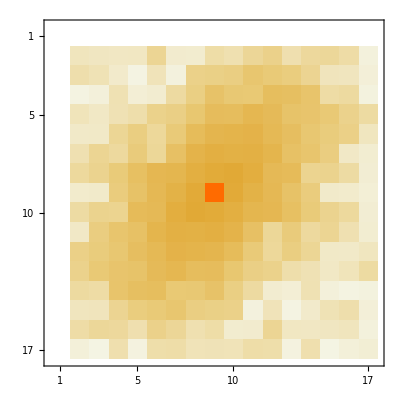

```mathematica
MatrixPlot[%9]
```

```mathematica
CorrFT = Fourier[Corr]
```

{{0.100023,-0.0849694,0.0744191,-0.0701657,0.0646437,-0.0627542,0.0594813,-0.0597186,0.0581043,-0.0597186,0.0594813,-0.0627542,0.0646437,-0.0701657,0.0744191,-0.0849694},{-0.0843518,0.0841705,-0.0772993,0.0714776,-0.0663308,0.0625629,-0.0598667,0.0589045,-0.0586209,0.0586611,-0.059221,0.0610154,-0.0634328,0.066574,-0.070611,0.0763682},{0.0734532,-0.0760007,0.0749877,-0.0713094,0.0671643,-0.0631893,0.0604838,-0.0586259,0.0580413,-0.0577358,0.0583125,-0.0597179,0.0613656,-0.0632232,0.0667987,-0.070805},{-0.0695495,0.0705251,-0.0708125,0.069376,-0.0669465,0.0636109,-0.0608066,0.0588229,-0.0576385,0.0576317,-0.0578015,0.0584858,-0.0597099,0.0612731,-0.0632416,0.0667811},{0.0642951,-0.0662034,0.0669531,-0.0664281,0.0654303,-0.0633129,0.0610088,-0.0590912,0.0579417,-0.0574698,0.0573432,-0.0573561,0.0583502,-0.0595835,0.0610651,-0.0629427},{-0.06235,0.0628395,-0.0639154,0.0645389,-0.0637887,0.0624379,-0.0605643,0.0590504,-0.0579902,0.057681,-0.0571387,0.0572129,-0.0573137,0.0580301,-0.0595906,0.0608609},{0.058901,-0.0603182,0.0615421,-0.0623417,0.0624514,-0.0613235,0.0602342,-0.0588695,0.0583805,-0.0580674,0.0576086,-0.0570853,0.0576559,-0.0578071,0.0584297,-0.0593909},{-0.0591557,0.0589648,-0.0591679,0.0600658,-0.0601801,0.0604763,-0.0599993,0.0591568,-0.0585241,0.0583765,-0.0581168,0.0576335,-0.0577879,0.0579561,-0.0581759,0.0584779},{0.0574917,-0.0583577,0.0586186,-0.0584329,0.0584289,-0.0586964,0.0590426,-0.0587067,0.0587158,-0.0587067,0.0590426,-0.0586964,0.0584289,-0.0584329,0.0586186,-0.0583577},{-0.0591557,0.0584779,-0.0581759,0.0579561,-0.0577879,0.0576335,-0.0581168,0.0583765,-0.0585241,0.0591568,-0.0599993,0.0604763,-0.0601801,0.0600658,-0.0591679,0.0589648},{0.058901,-0.0593909,0.0584297,-0.0578071,0.0576559,-0.0570853,0.0576086,-0.0580674,0.0583805,-0.0588695,0.0602342,-0.0613235,0.0624514,-0.0623417,0.0615421,-0.0603182},{-0.06235,0.0608609,-0.0595906,0.0580301,-0.0573137,0.0572129,-0.0571387,0.057681,-0.0579902,0.0590504,-0.0605643,0.0624379,-0.0637887,0.0645389,-0.0639154,0.0628395},{0.0642951,-0.0629427,0.0610651,-0.0595835,0.0583502,-0.0573561,0.0573432,-0.0574698,0.0579417,-0.0590912,0.0610088,-0.0633129,0.0654303,-0.0664281,0.0669531,-0.0662034},{-0.0695495,0.0667811,-0.0632416,0.0612731,-0.0597099,0.0584858,-0.0578015,0.0576317,-0.0576385,0.0588229,-0.0608066,0.0636109,-0.0669465,0.069376,-0.0708125,0.0705251},{0.0734532,-0.070805,0.0667987,-0.0632232,0.0613656,-0.0597179,0.0583125,-0.0577358,0.0580413,-0.0586259,0.0604838,-0.0631893,0.0671643,-0.0713094,0.0749877,-0.0760007},{-0.0843518,0.0763682,-0.070611,0.066574,-0.0634328,0.0610154,-0.059221,0.0586611,-0.0586209,0.0589045,-0.0598667,0.0625629,-0.0663308,0.0714776,-0.0772993,0.0841705}}

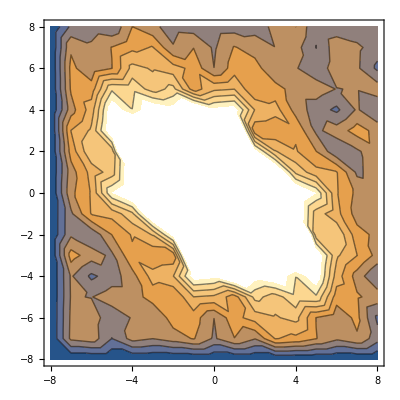

```mathematica
ListContourPlot[data]
```

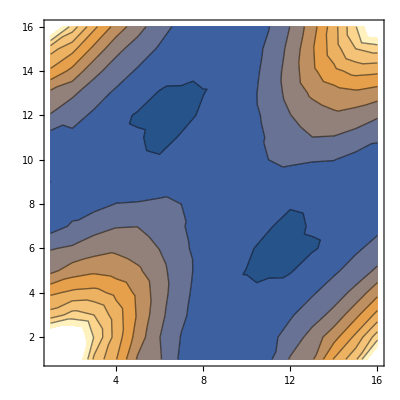

```mathematica
ListContourPlot[Abs[CorrFT]]
```